### Control test of UMAP

```mathematica
aps = Table[SeedRandom[222334+i];ArrayPlot[{CenterArray[Table[1, Round[RandomVariate[NormalDistribution[10, 5]]]],25]}, Mesh->True, ImageSize->{Automatic, 30}], {i, 400}];
```

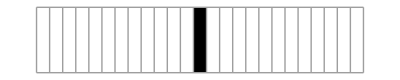
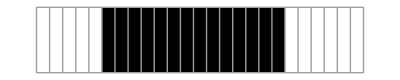
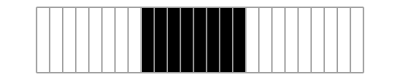
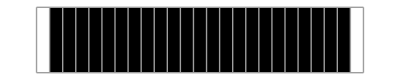
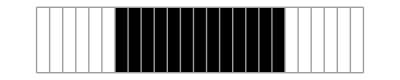
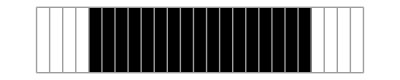
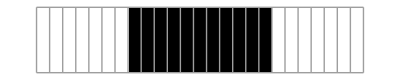
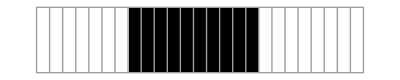
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aps[[;;10]]
```

```mathematica
RandomVariate[]
```

```mathematica
Round[RandomReal[{0, 1}]*1000]
```

527

```mathematica
disks = Table[SeedRandom[332111+i];Graphics[Join[{FaceForm[None], EdgeForm[Black]},{Disk[{0, 0}, Ramp[RandomVariate[NormalDistribution[10, 3]]]]}], PlotRange->20], {i, 1000}];
```

```mathematica
disks = Table[SeedRandom[332500+i];Graphics[Join[{FaceForm[{GrayLevel[.8], Opacity[.1]}], EdgeForm[GrayLevel[.3]]},{Disk[{0, 0}, Ramp[RandomVariate[NormalDistribution[10, 3]]]]}], PlotRange->20], {i, 1000}];
```

```mathematica
Show[disks]
```

-Graphics-

```mathematica
Rasterize/@disks[[;;3]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
rds = Rasterize/@ disks;
```

```mathematica
ByteCount[rds]
```

622300928

```mathematica
ByteCount[Rasterize/@disks]
```

$Aborted

```mathematica
FeatureSpacePlot[disks]
```

-Graphics-

```mathematica
FeatureSpacePlot[rds]
```

-Graphics-

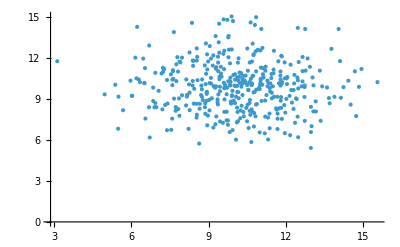

```mathematica
ListPlot[Ramp[RandomVariate[NormalDistribution[10, 2], {400, 2}]]]
```

```mathematica
FeatureSpacePlot[Random]
```

```mathematica
ResourceFunction["HistogramBubbleChart"][{#, 1}&/@Round[Ramp[RandomVariate[NormalDistribution[10, 2], 400]], .1]]
```

-Graphics-

```mathematica
ByteCount[]
```

1600

```mathematica
FeatureSpacePlot[aps]
```

-Graphics-

```mathematica
CenterArray[{1, 1}, 3]
```

{1,1,0}

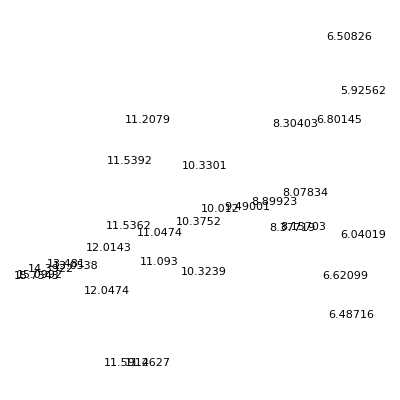

```mathematica
FeatureSpacePlot[Ramp[RandomVariate[NormalDistribution[10, 3], 30]]]
```

```mathematica
SeedRandom[333334];DimensionReduce[Ramp[RandomVariate[NormalDistribution[10, 3], 30]], 1];
SeedRandom[333334];
Ramp[RandomVariate[NormalDistribution[10, 3], 30]];
```

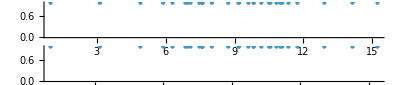

```mathematica
GraphicsColumn[With[{rands = Ramp[RandomVariate[NormalDistribution[10, 3], 30]]},
NumberLinePlot/@{rands, Catenate[DimensionReduce[rands, 1]]}
]]
```

```mathematica
FeatureSpacePlot[{1, 2, 3}, LabelingFunction->None]
```

-Graphics-

```mathematica
With[{rands = Ramp[RandomVariate[NormalDistribution[10, 3], {30, 2}]]},
NumberLinePlot/@{rands, Catenate[DimensionReduce[rands, 1]]}
]]
```

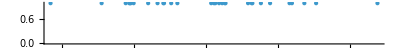

```mathematica
NumberLinePlot[Catenate[]]
```

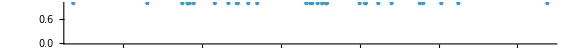

```mathematica
NumberLinePlot[]
```

### Incedence of disease based on human categorization of disease

```mathematica
hi = Import["/Users/erichegonzales/Projects/Wolfram/Biology/GrekaLab/IHME-GBD_2021_DATA-81721954-1.csv", "Tabular"]
```

```mathematica
ReverseSortBy[hi, #val&]
```

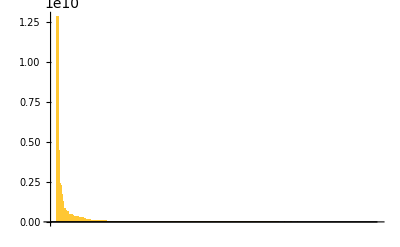

```mathematica
BarChart[ReverseSort[Normal[hi[[All, "val"]]]]]
```

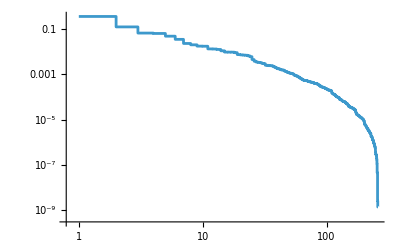

```mathematica
ListStepPlot[ReverseSort[Normal[hi[[All, "val"]]]] / Total[Normal[hi[[All, "val"]]]], ScalingFunctions->{"Log", "Log"}, PlotRange->All]
```

```mathematica
Normal[ReverseSortBy[hi, #val&][[All, {"cause_name", "val"}]]]
```

{<|cause_name→Upper respiratory infections,val→1.28223×10^10|>,<|cause_name→Diarrheal diseases,val→4.43858×10^9|>,<|cause_name→Caries of permanent teeth,val→2.37041×10^9|>,<|cause_name→COVID-19,val→2.27972×10^9|>,<|cause_name→Fungal skin diseases,val→1.72922×10^9|>,<|cause_name→Caries of deciduous teeth,val→1.25326×10^9|>,<|cause_name→Pyoderma,val→8.24863×10^8|>,<|cause_name→Tension-type headache,val→7.19043×10^8|>,<|cause_name→Other skin and subcutaneous diseases,val→6.29361×10^8|>,<|cause_name→Scabies,val→6.22474×10^8|>,<|cause_name→Other gynecological diseases,val→4.74521×10^8|>,<|cause_name→Vitamin A deficiency,val→4.69193×10^8|>,<|cause_name→Urinary tract infections and interstitial nephritis,val→4.49102×10^8|>,<|cause_name→Otitis media,val→3.91326×10^8|>,<|cause_name→Lower respiratory infections,val→3.43607×10^8|>,<|cause_name→Trichomoniasis,val→3.41916×10^8|>,<|cause_name→Major depressive disorder,val→3.41116×10^8|>,<|cause_name→Gastroesophageal reflux disease,val→3.2414×10^8|>,<|cause_name→Low back pain,val→2.66873×10^8|>,<|cause_name→Premenstrual syndrome,val→2.59098×10^8|>,<|cause_name→Contact dermatitis,val→2.53305×10^8|>,<|cause_name→Malaria,val→2.49117×10^8|>,<|cause_name→Chlamydial infection,val→2.3569×10^8|>,<|cause_name→Falls,val→2.15566×10^8|>,<|cause_name→Acute hepatitis A,val→1.6086×10^8|>,<|cause_name→Seborrhoeic dermatitis,val→1.3571×10^8|>,<|cause_name→Acne vulgaris,val→1.24266×10^8|>,<|cause_name→Other exposure to mechanical forces,val→1.20679×10^8|>,<|cause_name→Urticaria,val→1.17015×10^8|>,<|cause_name→Protein-energy malnutrition,val→1.08857×10^8|>,<|cause_name→Urolithiasis,val→1.05984×10^8|>,<|cause_name→Migraine,val→9.01834×10^7|>,<|cause_name→Periodontal diseases,val→8.96135×10^7|>,<|cause_name→Varicella and herpes zoster,val→8.66781×10^7|>,<|cause_name→Gonococcal infection,val→8.62773×10^7|>,<|cause_name→Viral skin diseases,val→8.47304×10^7|>,<|cause_name→Endocrine, metabolic, blood, and immune disorders,val→7.94739×10^7|>,<|cause_name→Gallbladder and biliary diseases,val→7.32469×10^7|>,<|cause_name→Total burden related to hepatitis B,val→6.85081×10^7|>,<|cause_name→Acute hepatitis B,val→6.35337×10^7|>,<|cause_name→Pruritus,val→6.25288×10^7|>,<|cause_name→Dengue,val→5.89642×10^7|>,<|cause_name→Cellulitis,val→5.59681×10^7|>,<|cause_name→Alcohol use disorders,val→5.57797×10^7|>,<|cause_name→Anxiety disorders,val→5.39174×10^7|>,<|cause_name→Total burden related to Non-alcoholic fatty liver disease (NAFLD),val→4.83533×10^7|>,<|cause_name→Nonalcoholic fatty liver disease including cirrhosis,val→4.8311×10^7|>,<|cause_name→Neck pain,val→4.32861×10^7|>,<|cause_name→Other unintentional injuries,val→4.29874×10^7|>,<|cause_name→Other benign and in situ neoplasms (internal),val→4.04208×10^7|>,<|cause_name→Genital herpes,val→4.01727×10^7|>,<|cause_name→Maternal abortion and miscarriage,val→3.86395×10^7|>,<|cause_name→Asthma,val→3.78642×10^7|>,<|cause_name→Non-venomous animal contact,val→3.50229×10^7|>,<|cause_name→Ischemic heart disease,val→3.18728×10^7|>,<|cause_name→Alopecia areata,val→3.0893×10^7|>,<|cause_name→Osteoarthritis knee,val→3.08459×10^7|>,<|cause_name→Foreign body in eyes,val→2.86702×10^7|>,<|cause_name→Gastritis and duodenitis,val→2.72025×10^7|>,<|cause_name→Edentulism,val→2.65273×10^7|>,<|cause_name→Diabetes mellitus type 2,val→2.39113×10^7|>,<|cause_name→Total cancers,val→2.35662×10^7|>,<|cause_name→Neonatal preterm birth,val→2.15538×10^7|>,<|cause_name→Physical violence by other means,val→2.09523×10^7|>,<|cause_name→Motor vehicle road injuries,val→1.95188×10^7|>,<|cause_name→Acute hepatitis E,val→1.93707×10^7|>,<|cause_name→Maternal sepsis and other maternal infections,val→1.90474×10^7|>,<|cause_name→G6PD trait,val→1.89341×10^7|>,<|cause_name→Syphilis,val→1.8696×10^7|>,<|cause_name→Maternal hypertensive disorders,val→1.80501×10^7|>,<|cause_name→Total Cancers excluding Non-melanoma skin cancer,val→1.72294×10^7|>,<|cause_name→Appendicitis,val→1.69636×10^7|>,<|cause_name→Chronic obstructive pulmonary disease,val→1.68954×10^7|>,<|cause_name→Dysthymia,val→1.63229×10^7|>,<|cause_name→Chronic kidney disease due to other and unspecified causes,val→1.61884×10^7|>,<|cause_name→Atopic dermatitis,val→1.60067×10^7|>,<|cause_name→Paralytic ileus and intestinal obstruction,val→1.57782×10^7|>,<|cause_name→Venomous animal contact,val→1.55249×10^7|>,<|cause_name→Conduct disorder,val→1.44841×10^7|>,<|cause_name→Genital prolapse,val→1.39717×10^7|>,<|cause_name→Maternal hemorrhage,val→1.39602×10^7|>,<|cause_name→Foreign body in other body part,val→1.39233×10^7|>,<|cause_name→Benign prostatic hyperplasia,val→1.37876×10^7|>,<|cause_name→Maternal obstructed labor and uterine rupture,val→1.34711×10^7|>,<|cause_name→Conflict and terrorism,val→1.25034×10^7|>,<|cause_name→Adverse effects of medical treatment,val→1.24813×10^7|>,<|cause_name→Total burden related to hepatitis C,val→1.16413×10^7|>,<|cause_name→Pedestrian road injuries,val→1.1521×10^7|>,<|cause_name→Osteoarthritis hand,val→1.03672×10^7|>,<|cause_name→Uterine fibroids,val→1.01003×10^7|>,<|cause_name→Lower extremity peripheral arterial disease,val→1.00388×10^7|>,<|cause_name→Alzheimer's disease and other dementias,val→9.83706×10^6|>,<|cause_name→Cyclist road injuries,val→9.76747×10^6|>,<|cause_name→Gout,val→9.40159×10^6|>,<|cause_name→Sickle cell trait,val→9.29397×10^6|>,<|cause_name→Fire, heat, and hot substances,val→9.19816×10^6|>,<|cause_name→G6PD deficiency,val→8.54877×10^6|>,<|cause_name→Ectopic pregnancy,val→8.37681×10^6|>,<|cause_name→Bulimia nervosa,val→8.22766×10^6|>,<|cause_name→Iodine deficiency,val→8.07984×10^6|>,<|cause_name→Drug-susceptible tuberculosis,val→7.93942×10^6|>,<|cause_name→Ischemic stroke,val→7.80445×10^6|>,<|cause_name→Inguinal, femoral, and abdominal hernia,val→7.24111×10^6|>,<|cause_name→Pertussis,val→7.22418×10^6|>,<|cause_name→Physical violence by sharp object,val→7.17957×10^6|>,<|cause_name→Typhoid fever,val→7.15456×10^6|>,<|cause_name→Acute hepatitis C,val→7.00991×10^6|>,<|cause_name→Other drug use disorders,val→6.75317×10^6|>,<|cause_name→Motorcyclist road injuries,val→6.70777×10^6|>,<|cause_name→Thalassemias trait,val→5.37994×10^6|>,<|cause_name→Self-harm by other specified means (internal),val→5.3719×10^6|>,<|cause_name→Psoriasis,val→5.09942×10^6|>,<|cause_name→Measles,val→4.81699×10^6|>,<|cause_name→Chronic hepatitis B including cirrhosis,val→4.76798×10^6|>,<|cause_name→Atrial fibrillation and flutter,val→4.48493×10^6|>,<|cause_name→Chronic hepatitis C including cirrhosis,val→4.47737×10^6|>,<|cause_name→Non-melanoma skin cancer (basal-cell carcinoma),val→4.43694×10^6|>,<|cause_name→Attention-deficit/hyperactivity disorder,val→4.11162×10^6|>,<|cause_name→Neonatal sepsis and other neonatal infections,val→3.88083×10^6|>,<|cause_name→Rheumatic heart disease,val→3.85469×10^6|>,<|cause_name→Cannabis use disorders,val→3.62551×10^6|>,<|cause_name→Osteoarthritis other,val→3.62223×10^6|>,<|cause_name→Endometriosis,val→3.44713×10^6|>,<|cause_name→Intracerebral hemorrhage,val→3.44434×10^6|>,<|cause_name→Environmental heat and cold exposure,val→3.42828×10^6|>,<|cause_name→Idiopathic epilepsy,val→3.27273×10^6|>,<|cause_name→Peptic ulcer disease,val→2.85437×10^6|>,<|cause_name→Other transport injuries,val→2.84333×10^6|>,<|cause_name→Police conflict and executions,val→2.75584×10^6|>,<|cause_name→Pancreatitis,val→2.74737×10^6|>,<|cause_name→Other road injuries,val→2.73066×10^6|>,<|cause_name→Bipolar disorder,val→2.564×10^6|>,<|cause_name→Decubitus ulcer,val→2.46832×10^6|>,<|cause_name→Congenital musculoskeletal and limb anomalies,val→2.43789×10^6|>,<|cause_name→Polycystic ovarian syndrome,val→2.30151×10^6|>,<|cause_name→Congenital heart anomalies,val→2.30033×10^6|>,<|cause_name→Tracheal, bronchus, and lung cancer,val→2.28069×10^6|>,<|cause_name→Meningitis,val→2.26486×10^6|>,<|cause_name→Colon and rectum cancer,val→2.19414×10^6|>,<|cause_name→Paratyphoid fever,val→2.16606×10^6|>,<|cause_name→Breast cancer,val→2.12156×10^6|>,<|cause_name→Chronic kidney disease due to diabetes mellitus type 2,val→2.01202×10^6|>,<|cause_name→Opioid use disorders,val→1.94253×10^6|>,<|cause_name→Non-melanoma skin cancer (squamous-cell carcinoma),val→1.89991×10^6|>,<|cause_name→Poisoning by other means,val→1.82421×10^6|>,<|cause_name→Osteoarthritis hip,val→1.79678×10^6|>,<|cause_name→Unintentional firearm injuries,val→1.78526×10^6|>,<|cause_name→HIV/AIDS resulting in other diseases,val→1.64533×10^6|>,<|cause_name→Benign and in situ intestinal neoplasms,val→1.55967×10^6|>,<|cause_name→Encephalitis,val→1.49277×10^6|>,<|cause_name→Vascular intestinal disorders,val→1.34702×10^6|>,<|cause_name→Parkinson's disease,val→1.33514×10^6|>,<|cause_name→Prostate cancer,val→1.32438×10^6|>,<|cause_name→Myocarditis,val→1.3197×10^6|>,<|cause_name→Chronic kidney disease due to hypertension,val→1.2822×10^6|>,<|cause_name→Anorexia nervosa,val→1.2673×10^6|>,<|cause_name→Physical violence by firearm,val→1.2666×10^6|>,<|cause_name→Pulmonary aspiration and foreign body in airway,val→1.24344×10^6|>,<|cause_name→Stomach cancer,val→1.23023×10^6|>,<|cause_name→Schizophrenia,val→1.22322×10^6|>,<|cause_name→Autism spectrum disorders,val→1.16371×10^6|>,<|cause_name→Non-rheumatic degenerative mitral valve disease,val→1.16256×10^6|>,<|cause_name→Urogenital congenital anomalies,val→1.09424×10^6|>,<|cause_name→Amphetamine use disorders,val→1.06901×10^6|>,<|cause_name→Cutaneous and mucocutaneous leishmaniasis,val→1.06664×10^6|>,<|cause_name→Neonatal encephalopathy due to birth asphyxia and trauma,val→1.06145×10^6|>,<|cause_name→Non-rheumatic calcific aortic valve disease,val→1.04437×10^6|>,<|cause_name→Endocarditis,val→1.04248×10^6|>,<|cause_name→Rheumatoid arthritis,val→1.00032×10^6|>,<|cause_name→HIV/AIDS - Drug-susceptible Tuberculosis,val→955221.|>,<|cause_name→Drowning,val→856135.|>,<|cause_name→Exposure to forces of nature,val→763059.|>,<|cause_name→Subarachnoid hemorrhage,val→697486.|>,<|cause_name→Cervical cancer,val→667426.|>,<|cause_name→Poisoning by carbon monoxide,val→600640.|>,<|cause_name→Benign and in situ cervical and uterine neoplasms,val→591855.|>,<|cause_name→Other non-Hodgkin lymphoma,val→585481.|>,<|cause_name→Esophageal cancer,val→576529.|>,<|cause_name→Hemolytic disease and other neonatal jaundice,val→566715.|>,<|cause_name→Bladder cancer,val→540310.|>,<|cause_name→Diabetes mellitus type 1,val→530859.|>,<|cause_name→Acute glomerulonephritis,val→528368.|>,<|cause_name→Sickle cell disorders,val→524217.|>,<|cause_name→Invasive Non-typhoidal Salmonella (iNTS),val→509976.|>,<|cause_name→Pancreatic cancer,val→508533.|>,<|cause_name→Uterine cancer,val→473614.|>,<|cause_name→Cirrhosis due to alcohol,val→462686.|>,<|cause_name→Digestive congenital anomalies,val→459018.|>,<|cause_name→Other chromosomal abnormalities,val→450742.|>,<|cause_name→Multidrug-resistant tuberculosis without extensive drug resistance,val→443680.|>,<|cause_name→Other malignant neoplasms,val→422295.|>,<|cause_name→Lip and oral cavity cancer,val→421577.|>,<|cause_name→Cirrhosis due to other causes,val→397989.|>,<|cause_name→Interstitial lung disease and pulmonary sarcoidosis,val→390267.|>,<|cause_name→Kidney cancer,val→387829.|>,<|cause_name→Inflammatory bowel disease,val→375140.|>,<|cause_name→Brain and central nervous system cancer,val→357482.|>,<|cause_name→Chronic kidney disease due to glomerulonephritis,val→357288.|>,<|cause_name→Myelodysplastic, myeloproliferative, and other hematopoietic neoplasms,val→341017.|>,<|cause_name→Malignant skin melanoma,val→303105.|>,<|cause_name→Ovarian cancer,val→298876.|>,<|cause_name→Thyroid cancer,val→249538.|>,<|cause_name→Cocaine use disorders,val→219145.|>,<|cause_name→Gallbladder and biliary tract cancer,val→216768.|>,<|cause_name→Other sense organ diseases,val→214543.|>,<|cause_name→Liver cancer due to hepatitis B,val→206366.|>,<|cause_name→Larynx cancer,val→200883.|>,<|cause_name→Orofacial clefts,val→183302.|>,<|cause_name→Other pharynx cancer,val→169820.|>,<|cause_name→Zika virus,val→169734.|>,<|cause_name→Chagas disease,val→160315.|>,<|cause_name→Liver cancer due to hepatitis C,val→154062.|>,<|cause_name→Multiple myeloma,val→148755.|>,<|cause_name→Cystic echinococcosis,val→148521.|>,<|cause_name→Acute myeloid leukemia,val→144646.|>,<|cause_name→Neural tube defects,val→120932.|>,<|cause_name→Thalassemias,val→119679.|>,<|cause_name→Nasopharynx cancer,val→118878.|>,<|cause_name→Chronic lymphoid leukemia,val→117987.|>,<|cause_name→Self-harm by firearm,val→115867.|>,<|cause_name→Acute lymphoid leukemia,val→103727.|>,<|cause_name→Liver cancer due to alcohol use,val→99543.7|>,<|cause_name→Soft tissue and other extraosseous sarcomas,val→96201.|>,<|cause_name→Chronic kidney disease due to diabetes mellitus type 1,val→95139.6|>,<|cause_name→Testicular cancer,val→91507.4|>,<|cause_name→Malignant neoplasm of bone and articular cartilage,val→91375.1|>,<|cause_name→Yellow fever,val→86509.|>,<|cause_name→Klinefelter syndrome,val→68357.5|>,<|cause_name→Hodgkin lymphoma,val→65182.|>,<|cause_name→Motor neuron disease,val→64177.7|>,<|cause_name→Multiple sclerosis,val→62920.1|>,<|cause_name→Down syndrome,val→59806.7|>,<|cause_name→Other leukemia,val→59231.9|>,<|cause_name→Tetanus,val→51191.5|>,<|cause_name→Leprosy,val→48054.6|>,<|cause_name→HIV/AIDS - Multidrug-resistant Tuberculosis without extensive drug resistance,val→45589.4|>,<|cause_name→Pulmonary Arterial Hypertension,val→43251.4|>,<|cause_name→Liver cancer due to NASH,val→42291.4|>,<|cause_name→Chronic myeloid leukemia,val→35830.9|>,<|cause_name→Silicosis,val→35482.9|>,<|cause_name→Mesothelioma,val→31907.9|>,<|cause_name→Visceral leishmaniasis,val→30217.7|>,<|cause_name→Other eye cancers,val→27675.8|>,<|cause_name→Extensively drug-resistant tuberculosis,val→24036.1|>,<|cause_name→Turner syndrome,val→23929.|>,<|cause_name→Liver cancer due to other causes,val→22891.7|>,<|cause_name→Burkitt lymphoma,val→19072.9|>,<|cause_name→Diphtheria,val→13312.9|>,<|cause_name→Neuroblastoma and other peripheral nervous cell tumors,val→10867.4|>,<|cause_name→Asbestosis,val→10520.3|>,<|cause_name→Rabies,val→10180.7|>,<|cause_name→Other pneumoconiosis,val→9407.53|>,<|cause_name→Coal workers pneumoconiosis,val→7455.71|>,<|cause_name→Retinoblastoma,val→6274.97|>,<|cause_name→Hepatoblastoma,val→4048.42|>,<|cause_name→African trypanosomiasis,val→1630.41|>,<|cause_name→HIV/AIDS - Extensively drug-resistant Tuberculosis,val→1606.42|>,<|cause_name→Ebola,val→93.9336|>,<|cause_name→Guinea worm disease,val→50.355|>,<|cause_name→Other mental disorders,val→0.|>,<|cause_name→Other neurological disorders,val→0.|>,<|cause_name→Other unspecified infectious diseases,val→0.|>,<|cause_name→Other sexually transmitted infections,val→0.|>}

```mathematica
ListStepPlot[Callout[#["val"], #["cause_name"]]&/@Normal[ReverseSortBy[hi, #val&][[All, {"cause_name", "val"}]]] , ScalingFunctions->{"Log", "Log"}, PlotRange->All]
```

-Graphics-

```mathematica
hi2 = Import["/Users/erichegonzales/Downloads/IHME-GBD_2021_DATA-772caba6-1/IHME-GBD_2021_DATA-772caba6-1.csv", "Tabular"]
```

```mathematica
ListStepPlot[Callout[#["val"] / Total[hi2[[All, "val"]]], #["cause"]]&/@Normal[ReverseSortBy[hi2, #val&][[All, {"cause", "val"}]]] , ScalingFunctions->{"Log", "Log"}, PlotRange->All]
```

-Graphics-

```mathematica
N[#val/Total[hi2[[All, "val"]]]]&/@Normal[ReverseSortBy[hi2, #val&][[All, {"cause", "val"}]]][[-10;;]]
```

{4.02675×10^-7,2.56773×10^-7,9.97602×10^-8,8.05467×10^-8,8.04857×10^-8,5.8692×10^-8,3.40321×10^-8,1.32994×10^-8,2.10661×10^-9,8.1299×10^-10}

```mathematica
(N[Values[ReverseSort[pcs]]/Total[Values[pcs]]])[[-10;;]]
```

{0.000228154,0.000228154,0.000228154,0.000228154,0.000228154,0.000228154,0.000228154,0.000228154,0.000228154,0.000228154}

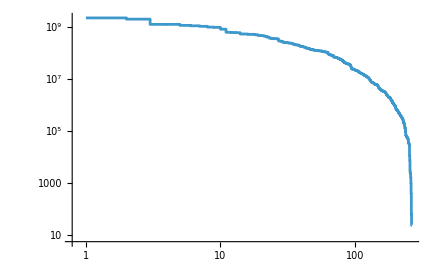

```mathematica
ListStepPlot[#val&/@Normal[ReverseSortBy[hi2, #val&][[All, {"cause", "val"}]]], ScalingFunctions->{"Log", "Log"}]
```

```mathematica
areas[[3]]
```

1459

```mathematica
Length[hi2]
```

263

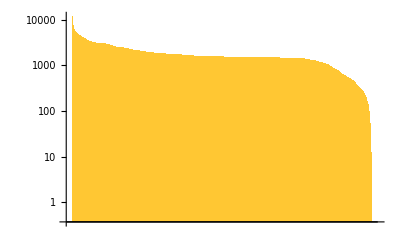

```mathematica
BarChart[ReverseSort[areas[[2;;]]/.Undefined->0], ScalingFunctions->{"Log", "Log"}]
```

```mathematica
Length[hi2]
```

263

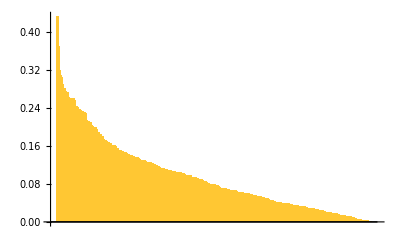

```mathematica
BarChart[ReverseSort[RandomVariate[HalfNormalDistribution[10], 263]]]
```

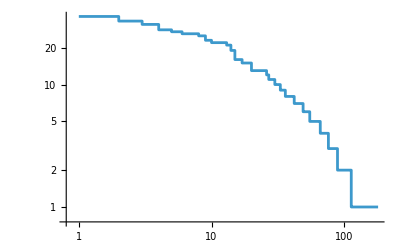

```mathematica
ListStepPlot[Values[ReverseSort[Counts[Round[RandomVariate[ParetoDistribution[100, 3], 1000]]]]], ScalingFunctions->{"Log", "Log"}, PlotRange->All]
```

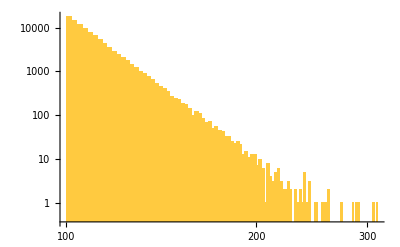

```mathematica
Histogram[RandomVariate[ParetoDistribution[100, 10], 100000], PlotRange->All, ScalingFunctions->{"Log", "Log"}]
```

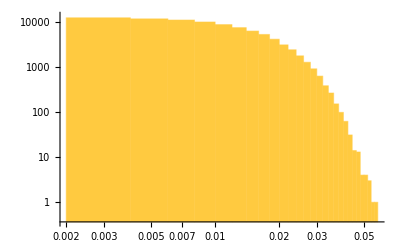

```mathematica
Histogram[RandomVariate[HalfNormalDistribution[100], 100000], PlotRange->All, ScalingFunctions->{"Log", "Log"}]
```

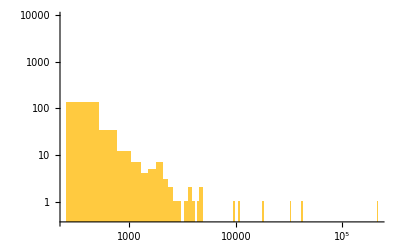

```mathematica
Histogram[RandomVariate[CauchyDistribution[100, 10], 10000], PlotRange->All, ScalingFunctions->{"Log", "Log"}]
```

```mathematica
polys=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-10,30}}},SeedRandom[6353];
ReverseSort@*Counts@*({{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&/@#&)@{{"[◼]", "allperts"}}[ru,init,txspec]];
```

```mathematica
Show[Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Dashed,Gray],Frame->True,FrameLabel->{"rank","frequency"}],ListStepPlot[Values[ReverseSort[polys]]/Total[Values[polys]],PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"rank","frequency"}]]
```

```mathematica
polys=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={400,{-100, 100}}},SeedRandom[6353];
({{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&/@#&)@{{"[◼]", "allperts"}}[ru,init,txspec]];
```

$Aborted

```mathematica
polys=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={400,{-100, 100}}},SeedRandom[6353];
ParallelMap[{{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&, {{"[◼]", "allperts"}}[ru,init,txspec]]];
```

```mathematica
pcs = ReverseSort[Counts[polys]];
```

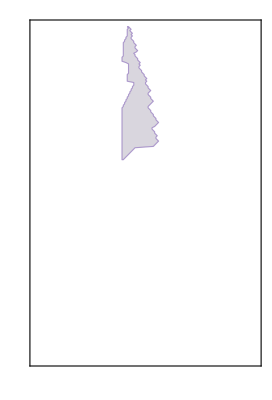
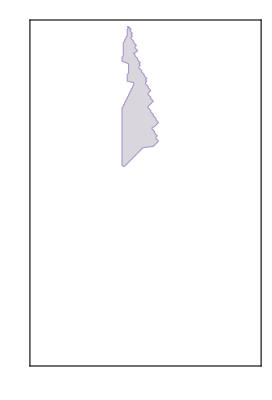
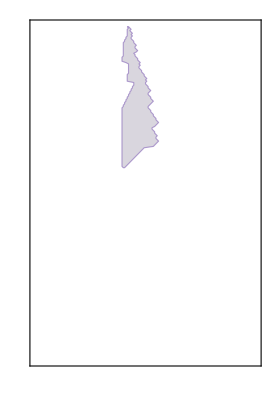
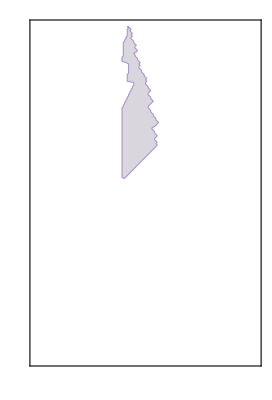
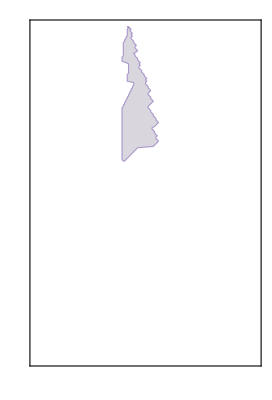
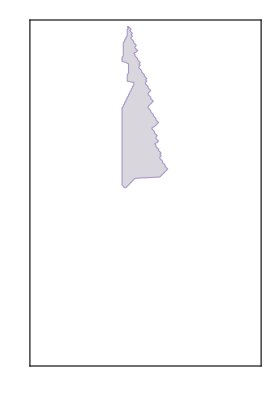
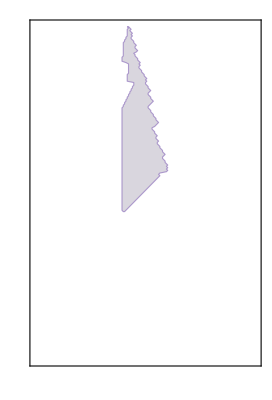
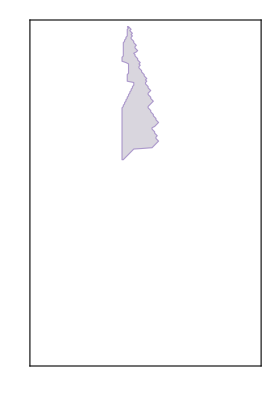

```mathematica
Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63](*AbsoluteDashing[{4,1}],*)(*AbsoluteThickness[1.25]*)}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3], #},Frame->True,FrameTicks->None,FrameStyle->GrayLevel[0,.25],ImageSize->{Automatic,200},PlotRange->{{30,200},{150,400}}]&/@ Keys[Take[pcs, 40]]
```

```mathematica
Length[pcs]
```

2423

```mathematica
Take[pcs, 10]
```

<|Polygon[…]→224,Polygon[…]→80,Polygon[…]→66,Polygon[…]→64,Polygon[…]→57,Polygon[…]→56,Polygon[…]→39,Polygon[…]→22,Polygon[…]→19,Polygon[…]→19|>

```mathematica
polys150=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={150,{-110,110}}},SeedRandom[6353];
Keys@*(RandomSample[Select[#,#==1&],60]&)@*ReverseSort@*Counts@*({{"[◼]", "CAPolygon"}}[Take[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False],All,{95,150}]]&/@#&)@{{"[◼]", "allperts"}}[ru,init,txspec]];
```

```mathematica
GraphicsGrid@*(Partition[SeedRandom[6353];#,(*20*)20]&)@*(Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63](*AbsoluteDashing[{4,1}],*)(*AbsoluteThickness[1.25]*)}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{0,60},{0,150}}]&/@#&)@SortBy[polys150,Area]
```

```mathematica
{EdgeForm[{Hue[0.73,0.43,0.72,0.63](*AbsoluteDashing[{4,1}],*)(*AbsoluteThickness[1.25]*)}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3]}
```

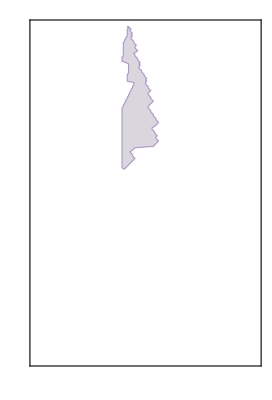
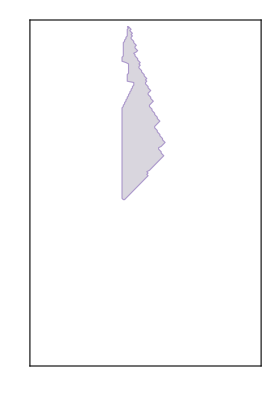
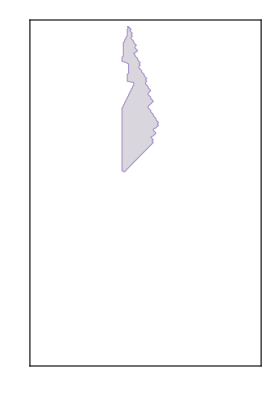
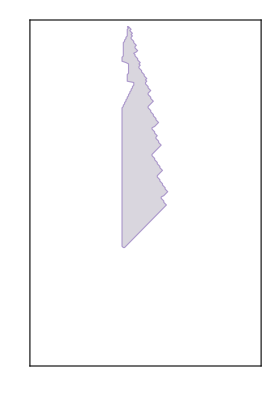
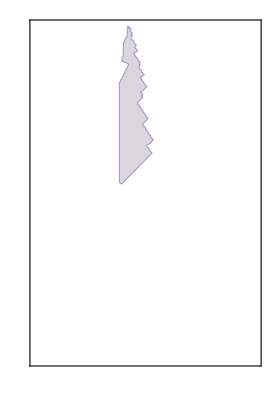
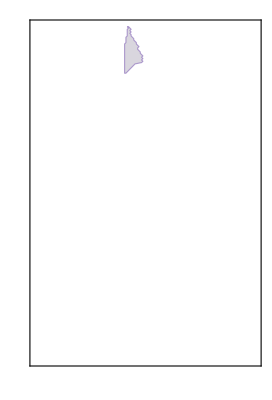
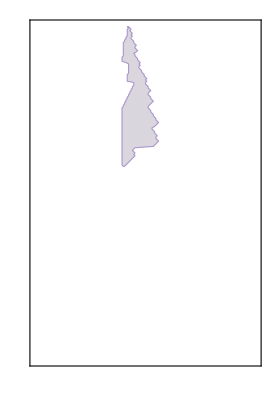
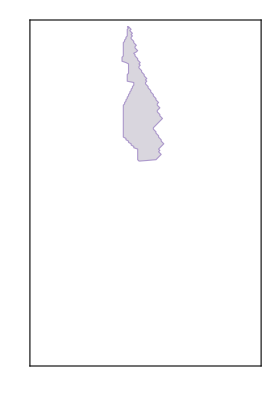
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63](*AbsoluteDashing[{4,1}],*)(*AbsoluteThickness[1.25]*)}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3], #},Frame->True,FrameTicks->None,FrameStyle->GrayLevel[0,.25],ImageSize->{Automatic,200},PlotRange->{{30,200},{150,400}}]&/@ RandomSample[polys, 30]
```

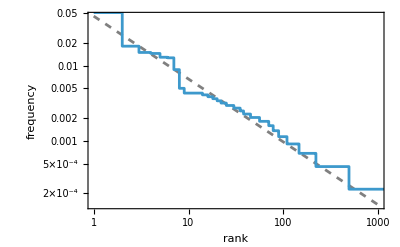

```mathematica
Show[Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Dashed,Gray],Frame->True,FrameLabel->{"rank","frequency"}],ListStepPlot[Values[ReverseSort[pcs]]/Total[Values[pcs]],PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"rank","frequency"}]]
```

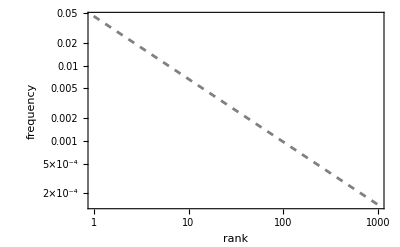

```mathematica
Show[Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Dashed,Gray],Frame->True,FrameLabel->{"rank","frequency"}],ListStepPlot[Values[ReverseSort[pcs]],PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"rank","frequency"}]]
```

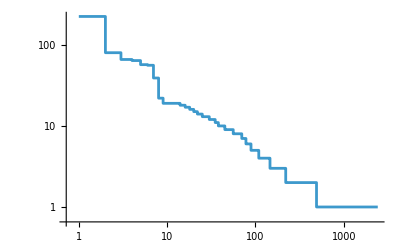

```mathematica
ListStepPlot[Values[ReverseSort[pcs]],ScalingFunctions->{"Log","Log"}]
```

```mathematica
2.2*10^-4
```

0.00022

```mathematica
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},Histogram[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ {{"[◼]", "allperts"}}[ru, init, txspec],  100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]]
```

```mathematica
lts = Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},ParallelMap[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, #, "ReturnPerturbations"->False]]&, {{"[◼]", "allperts"}}[ru, init, txspec]]];
```

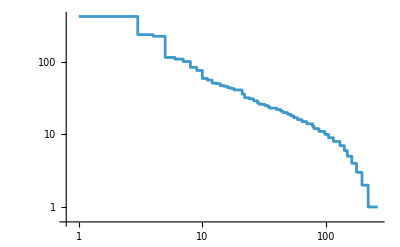

```mathematica
ListStepPlot[Values[ReverseSort[Counts[lts]]], ScalingFunctions->{"Log", "Log"}]
```

```mathematica
areas = ParallelMap[Area,polys];
```

$Aborted

```mathematica
areas = Area/@ polys;
```

```mathematica
ByteCount[areas]
```

107640

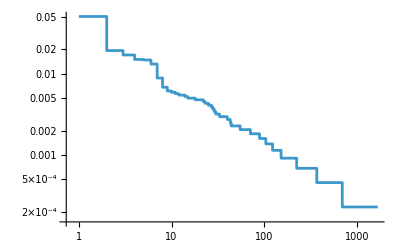

```mathematica
ListStepPlot[Values[ReverseSort[Counts[areas]]] / Total[Values[ReverseSort[Counts[areas]]]], ScalingFunctions->{"Log", "Log"}]
```

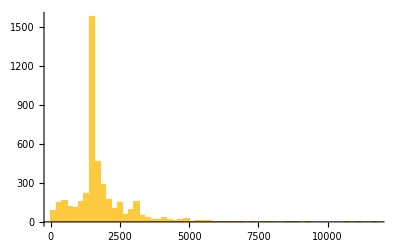

```mathematica
Histogram[areas, PlotRange->All]
```

### Testing distributions of other rules